```mathematica
Clear[sig2,sig22,l2,l1,s,c,a,b];
sig2 := ({{0, -I}, {I, 0}});
sig22 := ({{0, 0, 0, -1}, {0, 0, 1, 0}, {0, 1, 0, 0}, {-1, 0, 0, 0}});
l2[o_,r_] := E^(o √(1-1/r));
l1[o_,r_] := 1/l2[o,r];
s[o_,r_]:= 1/(√(1+l2[o,r]));
c[o_,r_]:= √(1-s[o,r]^2);
```

```mathematica
(*-------------------------------Subscript[ρ, AI]-----------------------------*)
Clear[rouAI,rouRouAI,eigRouAI,a,b];
rouAI[a_,b_,o_,r_] := ({{a^2 c[o,r]^2, 0, 0, a b c[o,r]}, {0, a^2 s[o,r]^2, 0, 0}, {0, 0, 0, 0}, {a b c[o,r], 0, 0, b^2}});Clear[c,s];
rouRouAI[a_,b_,o_,r_] = rouAI[a,b,o,r]. sig22.rouAI[a,b,o,r].sig22;
eigRouAI[a_,b_,o_,r_] = Simplify[Eigenvalues[rouRouAI[a,b,o,r]]]
```

{0,0,0,4 a^2 b^2 c[o,r]^2}

```mathematica
(*-------------------------------Subscript[ρ, AII]-----------------------------*)
Clear[rouAII,rouRouAII,eigRouAII,a,b];
rouAII[a_,b_,o_,r_] := ({{a^2 c[o,r]^2, 0, 0, 0}, {0, a^2 s[o,r]^2, a b s[o,r], 0}, {0, a b s[o,r], b^2, 0}, {0, 0, 0, 0}});Clear[c,s];
rouRouAII[a_,b_,o_,r_] = rouAII[a,b,o,r]. sig22.rouAII[a,b,o,r].sig22;
eigRouAII[a_,b_,o_,r_] = Simplify[Eigenvalues[rouRouAII[a,b,o,r]]]
```

{0,0,0,4 a^2 b^2 s[o,r]^2}

```mathematica
(*-------------------------------Subscript[ρ, III]-----------------------------*)
Clear[rouIII,rouRouIII,eigRouIII,a,b];
rouIII[a_,b_,o_,r_] := ({{a^2 c[o,r]^2, 0, 0, a^2 c[o,r]s[o,r]}, {0, 0, 0, 0}, {0, 0, b^2, 0}, {a^2 c[o,r]s[o,r], 0, 0, a^2 s[o,r]^2}});Clear[c,s];
rouRouIII[a_,b_,o_,r_] = rouIII[a,b,o,r]. sig22.rouIII[a,b,o,r].sig22
eigRouIII[a_,b_,o_,r_] = Simplify[Eigenvalues[rouRouIII[a,b,o,r]]]
```

{{2 a^4 c[o,r]^2 s[o,r]^2,0,0,2 a^4 c[o,r]^3 s[o,r]},{0,0,0,0},{0,0,0,0},{2 a^4 c[o,r] s[o,r]^3,0,0,2 a^4 c[o,r]^2 s[o,r]^2}}

{0,0,0,4 a^4 c[o,r]^2 s[o,r]^2}

```mathematica
(*--------------------W-----------------*)
Clear[rou,a,b,r,rouAC,rouAB,eigRouAC,eigRouAB,rouA];
rou[a_,b_,r_] = ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, r^2, r b, 0, r a, 0, 0, 0}, {0, b r, b^2, 0, b a, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, a r, a b, 0, a^2, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}} );
(*"rouAB is :"*)
rouAB[a_,b_,r_] = Simplify[Map[Tr,Partition[rou[a,b,r],{2,2}] ,{2}]];
rouAC[a_,b_,r_] = Join[Join[(rou[a,b,r][[1;;2,1;;2]]+rou[a,b,r][[3;;4,3;;4]]),(rou[a,b,r][[1;;2,5;;6]]+rou[a,b,r][[3;;4,7;;8]]),2],Join[(rou[a,b,r][[5;;6,1;;2]]+rou[a,b,r][[7;;8,3;;4]]),(rou[a,b,r][[5;;6,5;;6]]+rou[a,b,r][[7;;8,7;;8]]),2]];

eigRouAB = Simplify[Eigenvalues[rouAB[a,b,r].sig22.rouAB[a,b,r].sig22]]
eigRouAC = Simplify[Eigenvalues[rouAC[a,b,r].sig22.rouAC[a,b,r].sig22]]

"rouA is :"
rouA[a_,b_,r_] = Simplify[Map[Tr,Partition[rouAB[a,b,r],{2,2}] ,{2}]]
Sqrt[2(1-Tr[rouA[a,b,r].rouA[a,b,r]])];
```

{0,0,0,4 a^2 b^2}

{0,0,0,4 a^2 r^2}

rouA is :

{{b^2+r^2,0},{0,a^2}}

```mathematica
Clear[a];
NSolve[x^2-2 a^4 √E x +1 ==0,x]/. a->1/(√2)
```

{{x→0.41218-0.911102 ⅈ},{x→0.41218+0.911102 ⅈ}}

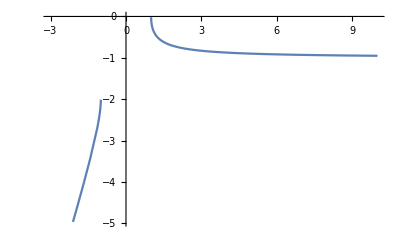

```mathematica
Plot[x-√(x^2-1)-1,{x,-3,10}]
```